```mathematica
index[n_Integer] := With[{t=n+1-Range[Mod[n-2,4]-1],
r=Select[Range[6,n],Mod[#,4]>1&]},
Range@Min[n,3]~Join~SortBy[r~Join~t,#~Mod~4&]];
(*--------------------------------------------------------------*)
coeff[n_Integer]:={{1,2},{1,1},{1,2},{2,3},{1,1+GoldenRatio},{1,3}}[[n]];
(*--------------------------------------------------------------*)
frames[polygon_List,steps_]:=Block[{c,g,p,r,start,mark,route,walk},
r=Range@Length[polygon];
mark={PointSize@Medium,Red,Point[#]}&;
p = ConstantArray[Graphics[],4steps];
start=Transpose@polygon//All~Query~{Min,Max}//RandomReal/@#&;
Do[
c=RandomChoice@r;
route={start,polygon[[c]]};
walk={start,(#[[1]]start+polygon[[c]])/#[[2]]}&[coeff@Last@r];
g={mark@start,Text[Style[c,Magenta,FontSize->36],{1.4,.9}],
{Blue,Dashed,Line@route},{LightRed,Thin,Line@walk}};
MapIndexed[p[[4i+#2]]~Set~#1&,Graphics/@g];
start=Last@walk,
{i,0,steps-1}];
g={Graphics@GraphicsComplex[polygon,Point@r],
ListPlot[Labeled[polygon[[#]],Text[#],Bottom]&/@r]};
g~Join~p~Append~Graphics@mark@start];
```

```mathematica
triangle={{0,1},{-1,-1},{1.5,-1}};
animate[steps_]:=frames[triangle,steps];
With[{a=animate[15]},
With[{f=Show[a[[index@#]],ImageSize->Large]&/@Range[2,Length@a]},
Export["userwalk.gif",f,"DisplayDurations"->.5]]];
Directory[]
```

```mathematica
With[{gif=Import["https://i.stack.imgur.com/KRiRX.gif"]},
Animate[Show[gif[[n]],ImageSize->Large],{n,1,Length@gif,1},
AnimationRunning->False,AnimationRate->.7]]
```

```mathematica
With[{a=animate[50]},
Animate[Show[a[[index@n]],ImageSize->Large],{n,2,Length@a,1},
AnimationRunning->False,AnimationRate->.7]]
```

#### Implementation of the Chaos Game

```mathematica
pointset=With[{n=10^6,bound=Transpose@triangle//All~Query~{Min,Max}},
NestList[(RandomChoice[triangle]+#)/2 &,RandomReal/@bound, n]];
```

```mathematica
game[steps_Integer] := Module[{p1, p2, p3,size},
size=(1+15Log[#,#/steps]^1.35)&[Length@pointset]/2.1;
p1={PointSize[Large],Darker@Green,Point[triangle]};
p2=Text[Style["steps" steps,Blue,FontSize->20],{1.2,.9}];
p3={AbsolutePointSize@size,Red,Point@pointset[[1;;steps]]};
Show[Graphics/@{p1, p2, p3},ImageSize->Large]]
```

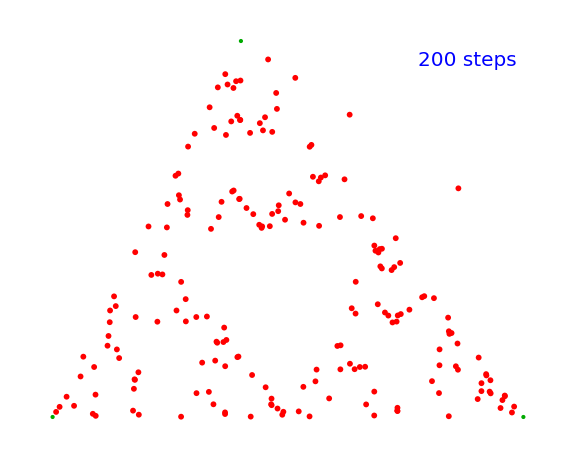

```mathematica
game[200]
```

```mathematica
Manipulate[game@Round[1.304^n],{n,2,52,1}]
```

```mathematica
With[{p=Join[1.304^Range[2,52],Length@pointset-{2,1}]},
With[{frames=game@Round[#]&/@p},
Export["game.gif",frames,"DisplayDurations"->.4]]];
```

#### Sierpiński carpet

```mathematica
pointset=With[{verts=DeleteCases[Tuples[{-1,0,1},{2}],{0,0}],n=10^6},
NestList[(2 RandomChoice[verts]+#)/3 &,RandomReal[{-1,1},2], n]];
```

```mathematica
carpet[n_Integer]:= Module[{ p1, p2,size},
size=(1+15Log[#,#/n]^1.13)&[Length@pointset]/2.1;
p1=Text[Style["steps" n, Darker@Green,FontSize -> 18],{0,0}];
p2={AbsolutePointSize@size,Blue,Point@pointset[[1;;n]]};
Show[Graphics/@{p1, p2},PlotRange->1.05, ImageSize -> Large]]
```

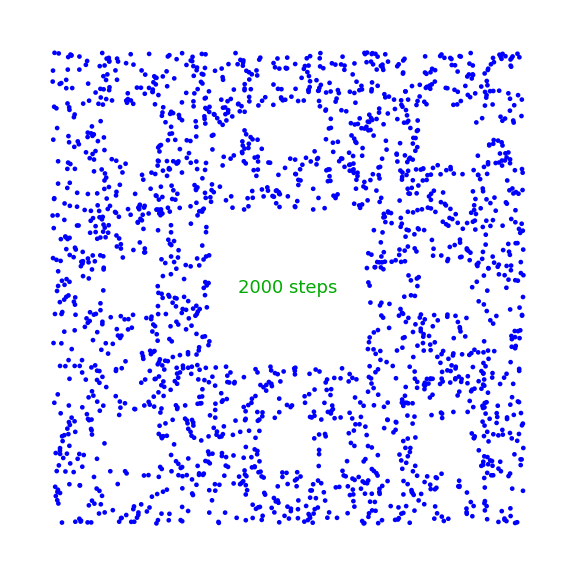

```mathematica
carpet[2000]
```

```mathematica
With[{p=Join[1.304^Range[2,52],Length@pointset-Range[9,1,-1]]},
With[{frames=carpet@Round[#]&/@p},
Export["carpet.gif",frames,"DisplayDurations"->.4]]];
```

#### Pentagonal Snowflake

```mathematica
pointset=With[{verts ={Cos[2 π #/5],Sin[2 π #/5]}&/@Range[5],n =10^6},
NestList[(RandomChoice[verts] + #)/(1 + GoldenRatio)&,
Transpose@verts//All~Query~{Min,Max}//RandomReal/@#&,n]];
```

```mathematica
flake5[n_Integer]:= Module[{r, p1, p2,size},
size=(1+15Log[#,#/n]^1.13)&[Length@pointset]/2.1;
r={Cos[2 π #/5],Sin[2 π #/5]}&/@Range[5];
r=Transpose[r]/GoldenRatio//All~Query~{Min,Max};
p1=Text[Style["steps" n, Darker@Green,FontSize -> 18],{0,0}];
p2={AbsolutePointSize@size,Blue,Point@pointset[[1;;n]]};
Show[Graphics[#,PlotRange->1.05r]&/@{p1, p2},ImageSize -> Large]]
```

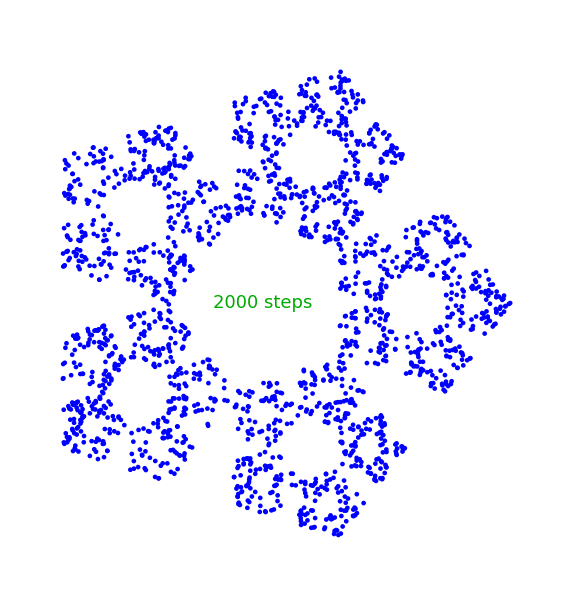

```mathematica
flake5[2000]
```

```mathematica
With[{p=Join[1.304^Range[2,52],Length@pointset-{2,1}]},
With[{frames=flake5@Round[#]&/@p},
Export["flake5.gif",frames,"DisplayDurations"->.4]]];
```

#### Hexagonal Snowflake

```mathematica
pointset=With[{verts ={Cos[2 π #/6],Sin[2 π #/6]}&/@Range[6],n =10^6},
NestList[(RandomChoice[verts] + #)/3&,
Transpose@verts//All~Query~{Min,Max}//RandomReal/@#&,n]];
```

```mathematica
flake6[n_Integer]:= Module[{r, p1, p2,size},
size=(1+15Log[#,#/n]^1.13)&[Length@pointset]/2.1;
r={Cos[2π #/6],Sin[2π #/6]}&/@Range[6];
r=Transpose[r]/2//All~Query~{Min,Max};
p1=Text[Style["steps" n, Darker@Green,FontSize -> 18],{0,0}];
p2={AbsolutePointSize@size,Blue,Point@pointset[[1;;n]]};
Show[Graphics[#,PlotRange->1.05r]&/@{p1, p2},ImageSize -> Large]]
```

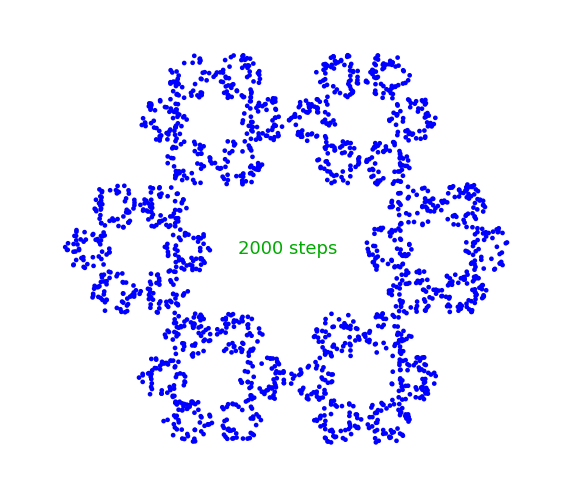

```mathematica
flake6[2000]
```

```mathematica
With[{p=Join[1.304^Range[2,52],Length@pointset-{2,1}]},
With[{frames=flake6@Round[#]&/@p},
Export["flake6.gif",frames,"DisplayDurations"->.4]]];
```